```mathematica
Clear["Global`*"];
```

```mathematica
a=1000;
```

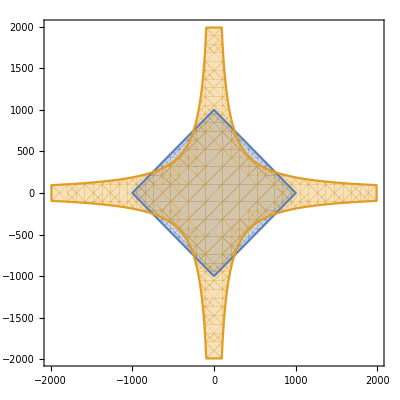

```mathematica
RegionPlot[{Abs[x]+Abs[y]<=a,Abs[x]*Abs[y]<=3/16*a^2},{x,-2*a,2*a},{y,-2*a,2*a},Mesh->{0}]
```

```mathematica
sol=Solve[{Abs[x]+Abs[y]==a&&Abs[x]*Abs[y]==3/16*a^2&&x>0&&y>0},{x,y}]
```

{{x→250,y→750},{x→750,y→250}}

```mathematica
x1=sol[[1,1,2]];
x2=sol[[2,1,2]];
```

```mathematica
area0=a^2/2-Integrate[(a-x)-3/16*a^2/x,{x,x1,x2}];
area=4*area0;
```

```mathematica
ans=Floor[area/100];
Print[ans];
```

18239